```mathematica
EmbedGraphInPlantri8b[key_]:=Block[{val=allGraphs5[key], sets, reference={1,2,3,4,5}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ plantri8,14];
g=EdgeDelete[ g,{1<->2,2<->3,3<->4,4<->5,5<->1}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
Table[ChromaticPolynomial[EmbedGraphInPlantri8b[k],4],{k,alfa1s}]
```

{72,192,0,192,72}

```mathematica
Table[PlanarGraphQ[EmbedGraphInPlantri8b[k]],{k,alfa1s}]
```

{False,False,False,False,False}

```mathematica
alfa1s
```

{36166,31738,29608,36112,31714}

```mathematica
Table[ShowGraph5Least[k],{k,alfa1s}]
```

{-Graphics-361660,-Graphics-317380,-Graphics-296080,-Graphics-361120,-Graphics-317140}

```mathematica
ChromaticPolynomial[EmbedGraphInPlantri8b[29608],4]
```

0

```mathematica
emb=EmbedGraphInPlantri8b[29608]
```

```mathematica
emb2=EmbedGraphInPlantri8b[31714]
```

```mathematica
FindClique[emb]
```

{{12,13,7}}

```mathematica
FindClique[emb2]
```

{{11,16,1,3}}

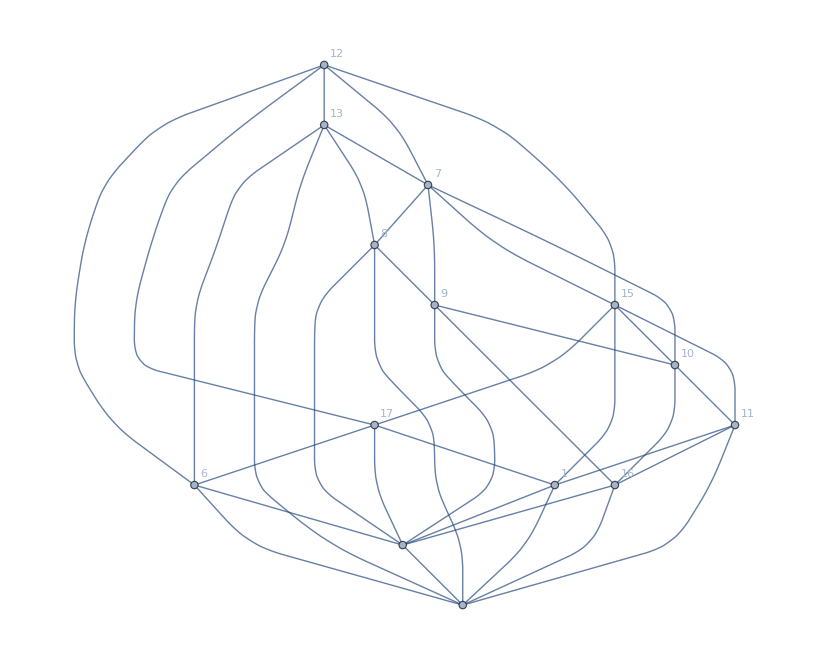

```mathematica
Graph[emb,GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
FindFullFormula5[emb]//Length
```

1586

```mathematica
1586/120
```

793/60

```mathematica
ChromaticPolynomial[EmbedGraphInPlantri8b[29608],5]/120
```

1586

```mathematica
CompleteBaseCoeff[ ChromaticPolynomial[emb,x]]
```

{0,0,0,0,0,1586,33088,146892,231967,163709,57997,10874,1080,53,1}

```mathematica
Length[Subsets[VertexList[emb],{5}]]
```

2002

```mathematica
VertexCount[emb]
```

14

```mathematica
EdgeCount[emb]
```

38

```mathematica
3*14-6
```

36

```mathematica
TableForm[
Monitor[
Table[
With[{emb=EmbedGraphInPlantri8b[k]},
Table[EdgeCount[Subgraph[emb,vert]],{vert,Subsets[VertexList[emb],{8}]}]//Tally//Sort
],
{k,alfa1s}
],
{k,vert}
],TableDepth->2
]
```

{7,7} | {8,67} | {9,179} | {10,452} | {11,681} | {12,675} | {13,529} | {14,292} | {15,100} | {16,17} | {17,4}
{8,29} | {9,180} | {10,463} | {11,701} | {12,767} | {13,503} | {14,245} | {15,97} | {16,15} | {17,3} | 
{8,36} | {9,135} | {10,472} | {11,740} | {12,741} | {13,545} | {14,250} | {15,72} | {16,12} |  | 
{8,29} | {9,180} | {10,463} | {11,701} | {12,767} | {13,503} | {14,245} | {15,97} | {16,15} | {17,3} | 
{7,7} | {8,67} | {9,179} | {10,452} | {11,681} | {12,675} | {13,529} | {14,292} | {15,100} | {16,17} | {17,4}

```mathematica
With[{f1=FindFullFormula5[emb],f2=FindFullFormula5[emb2]},
{Length[f1],Length[f2],Length[Intersection[f1,f2]]}
]
```

{1586,1657,390}

```mathematica
FactorInteger[{1586,1657,390}]
```

{{{2,1},{13,1},{61,1}},{{1657,1}},{{2,1},{3,1},{5,1},{13,1}}}

```mathematica
With[
{graphs=Append[Join[alfa1s,quads],lambdaKey]},
Block[{forms=Monitor[Table[FindFullFormula4[EmbedGraphInPlantri8b[k]],{k,graphs}],k], 
head=Table[With[{s=ShowGraph5Least[k]},If[k==29608,Framed[s],s]],{k,graphs}],
head2=Table[With[{s=Rotate[k,Pi/2]},If[k==29608,Framed[s],s]],{k,graphs}]},
Monitor[
TableForm[
Table[
Table[
Length[Intersection[forms[[i]],forms[[j]]]]
,{i,Length[forms]}
]
,{j,Length[forms]}
],
TableHeadings->{head, head2}
],
{i,j}
]
]
]
```

| 36166 | 31738 | 29608 | 36112 | 31714 | 36085 | 29605 | 29527 | 31711 | 29551 | 20665
-Graphics-361660 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-317380 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-296080 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-361120 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-317140 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-360850 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 0 | 0
-Graphics-296050 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0
-Graphics-295270 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 3 | 0
-Graphics-317110 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0
-Graphics-295510 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 11 | 0
-Graphics-206653 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 63

```mathematica
allGraphs5[alfa1Key,"vertexsets"]
```

{{1,3},{2,4},{5}}

```mathematica
Keys[allGraphs5[alfa1Key]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofournull,colofourrealnull,atleast,atleastwhy,embed,colofourgenerator,colotree}

```mathematica
EdgeUpgrade[sols_,key_]:=Block[{edges, result = sols},
edges=Select[allGraphs5[key,"vertexsets"],Length[#]==2&];
edges=Map[UndirectedEdge[#[[1]],#[[2]]]&,edges];
Table[
sols=Map[SymbolReplace[#,e]&,sols]
,{e,edges}
];
sols
]
```

```mathematica
SymbolReplace[v123,3<->4]
```

v1234

```mathematica
EmbedGraphInPlantri8b[alfa1Key]
```

```mathematica
IntegerDigits[VertexList[EmbedGraphInPlantri8b[alfa1Key]],32]
```

{{12},{13},{7},{15},{17},{6},{8},{9},{10},{11},{16},{5},{1},{2}}

```mathematica
FindFullFormula5[EmbedGraphInPlantri8b[alfa1Key]]
```

```mathematica
EdgeUpgrade[FindFullFormula5[EmbedGraphInPlantri8b[alfa1Key]],alfa1Key]
```

{{1,3},{2,4}}

{1<->3,2<->4}

```mathematica
With[
{graphs=alfa1s},
Block[{forms=Monitor[Table[EdgeUpgrade[FindFullFormula5[EmbedGraphInPlantri8b[kkk]],kkk],{kkk,graphs}],kkk], 
head=Table[With[{s=ShowGraph5Least[k]},If[k==29608,Framed[s],s]],{k,graphs}],
head2=Table[With[{s=Rotate[k,Pi/2]},If[k==29608,Framed[s],s]],{k,graphs}]},
Monitor[
TableForm[
Table[
Table[
Length[Intersection[forms[[i]],forms[[j]]]]
,{i,Length[forms]}
]
,{j,Length[forms]}
],
TableHeadings->{head, head2}
],
{i,j}
]
]
]
```

{{1,3},{2,4}}

{1<->3,2<->4}

{{1,4},{2,5}}

{1<->4,2<->5}

{{2,4},{3,5}}

{2<->4,3<->5}

{{1,3},{2,5}}

{1<->3,2<->5}

{{1,4},{3,5}}

{1<->4,3<->5}

| 36166 | 31738 | 29608 | 36112 | 31714
-Graphics-361660 | 1657 | 0 | 0 | 0 | 0
-Graphics-317380 | 0 | 1947 | 213 | 0 | 592
-Graphics-296080 | 0 | 213 | 1586 | 0 | 390
-Graphics-361120 | 0 | 0 | 0 | 1947 | 0
-Graphics-317140 | 0 | 592 | 390 | 0 | 1657

```mathematica
With[
{graphs=Append[Join[alfa1s,quads],lambdaKey]},
Block[{forms=Monitor[Table[EdgeUpgrade[FindFullFormula5[EmbedGraphInPlantri8b[kkk]],kkk],{kkk,graphs}],kkk], 
head=Table[With[{s=ShowGraph5Least[k]},If[k==29608,Framed[s],s]],{k,graphs}],
head2=Table[With[{s=Rotate[k,Pi/2]},If[k==29608,Framed[s],s]],{k,graphs}]},
Monitor[
TableForm[
Table[
Table[
Length[Intersection[forms[[i]],forms[[j]]]]
,{i,Length[forms]}
]
,{j,Length[forms]}
],
TableHeadings->{head, head2}
],
{i,j}
]
]
]
```

| 36166 | 31738 | 29608 | 36112 | 31714 | 36085 | 29605 | 29527 | 31711 | 29551 | 20665
-Graphics-361660 | 1657 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1657
-Graphics-317380 | 0 | 1947 | 213 | 0 | 592 | 0 | 0 | 0 | 0 | 0 | 1947
-Graphics-296080 | 0 | 213 | 1586 | 0 | 390 | 0 | 0 | 0 | 0 | 0 | 1586
-Graphics-361120 | 0 | 0 | 0 | 1947 | 0 | 0 | 0 | 0 | 0 | 0 | 1947
-Graphics-317140 | 0 | 592 | 390 | 0 | 1657 | 0 | 0 | 0 | 0 | 0 | 1657
-Graphics-360850 | 0 | 0 | 0 | 0 | 0 | 3696 | 0 | 0 | 0 | 0 | 3696
-Graphics-296050 | 0 | 0 | 0 | 0 | 0 | 0 | 3551 | 0 | 810 | 0 | 3551
-Graphics-295270 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3551 | 0 | 1613 | 3551
-Graphics-317110 | 0 | 0 | 0 | 0 | 0 | 0 | 810 | 0 | 3696 | 0 | 3696
-Graphics-295510 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1613 | 0 | 4136 | 4136
-Graphics-206653 | 1657 | 1947 | 1586 | 1947 | 1657 | 3696 | 3551 | 3551 | 3696 | 4136 | 31366

```mathematica
With[
{graphs=Append[Join[alfa1s,quads],lambdaKey]},
Block[{forms=Monitor[Table[EdgeUpgrade[FindFullFormula4[EmbedGraphInPlantri8b[kkk]],kkk],{kkk,graphs}],kkk], 
head=Table[With[{s=ShowGraph5Least[k]},If[k==29608,Framed[s],s]],{k,graphs}],
head2=Table[With[{s=Rotate[k,Pi/2]},If[k==29608,Framed[s],s]],{k,graphs}]},
Monitor[
TableForm[
Table[
Table[
Length[Intersection[forms[[i]],forms[[j]]]]
,{i,Length[forms]}
]
,{j,Length[forms]}
],
TableHeadings->{head, head2}
],
{i,j}
]
]
]
```

| 36166 | 31738 | 29608 | 36112 | 31714 | 36085 | 29605 | 29527 | 31711 | 29551 | 20665
-Graphics-361660 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3
-Graphics-317380 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8
-Graphics-296080 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-361120 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 8
-Graphics-317140 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3
-Graphics-360850 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 0 | 9
-Graphics-296050 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 6
-Graphics-295270 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 3 | 6
-Graphics-317110 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 9
-Graphics-295510 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 11 | 11
-Graphics-206653 | 3 | 8 | 0 | 8 | 3 | 9 | 6 | 6 | 9 | 11 | 63

```mathematica
With[
{graphs=Append[Append[Join[alfa1s,quads],K5Key],lambdaKey]},
Block[{forms=Monitor[Table[EdgeUpgrade[FindFullFormula5[EmbedGraphInPlantri8b[kkk]],kkk],{kkk,graphs}],kkk], 
head=Table[With[{s=ShowGraph5Least[k]},If[k==29608,Framed[s],s]],{k,graphs}],
head2=Table[With[{s=Rotate[k,Pi/2]},If[k==29608,Framed[s],s]],{k,graphs}]},
Monitor[
TableForm[
Table[
Table[
Length[Intersection[forms[[i]],forms[[j]]]]
,{i,Length[forms]}
]
,{j,Length[forms]}
],
TableHeadings->{head, head2}
],
{i,j}
]
]
]
```

| 36166 | 31738 | 29608 | 36112 | 31714 | 36085 | 29605 | 29527 | 31711 | 29551 | 29524 | 20665
-Graphics-361660 | 1657 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1657
-Graphics-317380 | 0 | 1947 | 213 | 0 | 592 | 0 | 0 | 0 | 0 | 0 | 0 | 1947
-Graphics-296080 | 0 | 213 | 1586 | 0 | 390 | 0 | 0 | 0 | 0 | 0 | 0 | 1586
-Graphics-361120 | 0 | 0 | 0 | 1947 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1947
-Graphics-317140 | 0 | 592 | 390 | 0 | 1657 | 0 | 0 | 0 | 0 | 0 | 0 | 1657
-Graphics-360850 | 0 | 0 | 0 | 0 | 0 | 3696 | 0 | 0 | 0 | 0 | 0 | 3696
-Graphics-296050 | 0 | 0 | 0 | 0 | 0 | 0 | 3551 | 0 | 810 | 0 | 0 | 3551
-Graphics-295270 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3551 | 0 | 1613 | 0 | 3551
-Graphics-317110 | 0 | 0 | 0 | 0 | 0 | 0 | 810 | 0 | 3696 | 0 | 0 | 3696
-Graphics-295510 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1613 | 0 | 4136 | 0 | 4136
-Graphics-295240 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3942 | 3942
-Graphics-206653 | 1657 | 1947 | 1586 | 1947 | 1657 | 3696 | 3551 | 3551 | 3696 | 4136 | 3942 | 31366

```mathematica
FindFullFormulaN[EmbedGraphInPlantri8b[K5Key],6]//Length
```

216502

```mathematica
Total[{1657,1947,1586,1947,1657,3696,3551,3551,3696,4136}]
```

```mathematica
27424+3942
```

31366

```mathematica
Total[{3,8,0,8,3,9,6,6,9,11}]
```

63

```mathematica
With[
{graphs=Append[Join[alfa1s,quads],lambdaKey]},
Block[{forms=Monitor[Table[EdgeUpgrade[FindFullFormula1234[EmbedGraphInPlantri8b[kkk]],kkk],{kkk,graphs}],kkk], 
head=Table[With[{s=ShowGraph5Least[k]},If[k==29608,Framed[s],s]],{k,graphs}],
head2=Table[With[{s=Rotate[k,Pi/2]},If[k==29608,Framed[s],s]],{k,graphs}]},
Monitor[
TableForm[
Table[
Table[
Length[Intersection[forms[[i]],forms[[j]]]]
,{i,Length[forms]}
]
,{j,Length[forms]}
],
TableHeadings->{head, head2}
],
{i,j}
]
]
]
```

| 36166 | 31738 | 29608 | 36112 | 31714 | 36085 | 29605 | 29527 | 31711 | 29551 | 20665
-Graphics-361660 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3
-Graphics-317380 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8
-Graphics-296080 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-361120 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 8
-Graphics-317140 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3
-Graphics-360850 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 0 | 9
-Graphics-296050 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 6
-Graphics-295270 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 3 | 6
-Graphics-317110 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 9
-Graphics-295510 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 11 | 11
-Graphics-206653 | 3 | 8 | 0 | 8 | 3 | 9 | 6 | 6 | 9 | 11 | 63

```mathematica
With[
{graphs=Append[Append[Join[alfa1s,quads],K5Key],lambdaKey]},
Block[{forms=Monitor[Table[EdgeUpgrade[FindFullFormulaN[EmbedGraphInPlantri8b[kkk],6],kkk],{kkk,graphs}],kkk], 
head=Table[With[{s=ShowGraph5Least[k]},If[k==29608,Framed[s],s]],{k,graphs}],
head2=Table[With[{s=Rotate[k,Pi/2]},If[k==29608,Framed[s],s]],{k,graphs}]},
Monitor[
TableForm[
Table[
Table[
Length[Intersection[forms[[i]],forms[[j]]]]
,{i,Length[forms]}
]
,{j,Length[forms]}
],
TableHeadings->{head, head2}
],
{i,j}
]
]
]
```

| 36166 | 31738 | 29608 | 36112 | 31714 | 36085 | 29605 | 29527 | 31711 | 29551 | 29524 | 20665
-Graphics-361660 | 33021 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 33021
-Graphics-317380 | 0 | 34494 | 8919 | 0 | 17125 | 0 | 0 | 0 | 0 | 0 | 0 | 34494
-Graphics-296080 | 0 | 8919 | 33088 | 0 | 12930 | 0 | 0 | 0 | 0 | 0 | 0 | 33088
-Graphics-361120 | 0 | 0 | 0 | 34494 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 34494
-Graphics-317140 | 0 | 17125 | 12930 | 0 | 33021 | 0 | 0 | 0 | 0 | 0 | 0 | 33021
-Graphics-360850 | 0 | 0 | 0 | 0 | 0 | 103438 | 0 | 0 | 0 | 0 | 0 | 103438
-Graphics-296050 | 0 | 0 | 0 | 0 | 0 | 0 | 103568 | 0 | 39648 | 0 | 0 | 103568
-Graphics-295270 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 103568 | 0 | 56941 | 0 | 103568
-Graphics-317110 | 0 | 0 | 0 | 0 | 0 | 0 | 39648 | 0 | 103438 | 0 | 0 | 103438
-Graphics-295510 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 56941 | 0 | 108277 | 0 | 108277
-Graphics-295240 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 216502 | 216502
-Graphics-206653 | 33021 | 34494 | 33088 | 34494 | 33021 | 103438 | 103568 | 103568 | 103438 | 108277 | 216502 | 906909

```mathematica
VertexCount[plantri8]
```

17

```mathematica
With[
{graphs=Append[Append[Join[alfa1s,quads],K5Key],lambdaKey]},
Block[{forms=Monitor[Table[EdgeUpgrade[FindFullFormulaN[EmbedGraphInPlantri8b[kkk],7],kkk],{kkk,graphs}],kkk], 
head=Table[With[{s=ShowGraph5Least[k]},If[k==29608,Framed[s],s]],{k,graphs}],
head2=Table[With[{s=Rotate[k,Pi/2]},If[k==29608,Framed[s],s]],{k,graphs}]},
Monitor[
TableForm[
Table[
Table[
Length[Intersection[forms[[i]],forms[[j]]]]
,{i,Length[forms]}
]
,{j,Length[forms]}
],
TableHeadings->{head, head2}
],
{i,j}
]
]
]
```

| 36166 | 31738 | 29608 | 36112 | 31714 | 36085 | 29605 | 29527 | 31711 | 29551 | 29524 | 20665
-Graphics-361660 | 145463 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 145463
-Graphics-317380 | 0 | 147410 | 57339 | 0 | 91205 | 0 | 0 | 0 | 0 | 0 | 0 | 147410
-Graphics-296080 | 0 | 57339 | 146892 | 0 | 74100 | 0 | 0 | 0 | 0 | 0 | 0 | 146892
-Graphics-361120 | 0 | 0 | 0 | 147410 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 147410
-Graphics-317140 | 0 | 91205 | 74100 | 0 | 145463 | 0 | 0 | 0 | 0 | 0 | 0 | 145463
-Graphics-360850 | 0 | 0 | 0 | 0 | 0 | 619374 | 0 | 0 | 0 | 0 | 0 | 619374
-Graphics-296050 | 0 | 0 | 0 | 0 | 0 | 0 | 625157 | 0 | 310324 | 0 | 0 | 625157
-Graphics-295270 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 625157 | 0 | 397327 | 0 | 625157
-Graphics-317110 | 0 | 0 | 0 | 0 | 0 | 0 | 310324 | 0 | 619374 | 0 | 0 | 619374
-Graphics-295510 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 397327 | 0 | 634418 | 0 | 634418
-Graphics-295240 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1995260 | 1995260
-Graphics-206653 | 145463 | 147410 | 146892 | 147410 | 145463 | 619374 | 625157 | 625157 | 619374 | 634418 | 1995260 | 5851378

```mathematica
With[
{graphs=Append[Append[Join[alfa1s,quads],K5Key],lambdaKey]},
Block[{forms=Monitor[Table[EdgeUpgrade[FindFullFormulaN[EmbedGraphInPlantri8b[kkk],15],kkk],{kkk,graphs}],kkk], 
head=Table[With[{s=ShowGraph5Least[k]},If[k==29608,Framed[s],s]],{k,graphs}],
head2=Table[With[{s=Rotate[k,Pi/2]},If[k==29608,Framed[s],s]],{k,graphs}]},
Monitor[
TableForm[
Table[
Table[
Length[Intersection[forms[[i]],forms[[j]]]]
,{i,Length[forms]}
]
,{j,Length[forms]}
],
TableHeadings->{head, head2}
],
{i,j}
]
]
]
```